# Euclidean Geometry (sample)

Init

```mathematica
SetDirectory[NotebookDirectory[]]
<<GeometrySceneDrawer.m
<<GeometryConjectureNew.m
<<SceneExamples.m
$EntityStores={};
PrependTo[$EntityStores,EntityFramework`$SceneExample]
```

C:\Users\nicolasr\Documents\PlaneGeometryDemo_Nov172017

{AffineHull,Angle,AngleBisector,CircleThrough,Collinear,Coplanar,Concurrent,Convex,Cyclic,EqualAngles,Equiangular,Equilateral,GeometricPoint,GeometricScene,InfiniteLineThrough,Inradius,LineThrough,Midpoint,Parallel,PerpendicularBisector,Radius,RegionCenter,Regular,Similar,Tangent,Unspecified,FindGeometricSceneGraphics,GeometricSceneToGraphicsPrimitives,FindGeometricCoordinates}

{FindGeometricConjectures}

{EntityFramework`$SceneExample}

{EntityStore[…]}

Example 1/110

```mathematica
hyp001={
Triangle[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"]}],
GeometricPoint["F"]==Midpoint[Line[{GeometricPoint["B"],GeometricPoint["C"]}]],
Collinear[GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["D"]],
Perpendicular[Line[{GeometricPoint["C"],GeometricPoint["D"]}],Line[{GeometricPoint["A"],GeometricPoint["B"]}]],
Collinear[GeometricPoint["A"],GeometricPoint["C"],GeometricPoint["E"]],
Perpendicular[Line[{GeometricPoint["B"],GeometricPoint["E"]}],Line[{GeometricPoint["A"],GeometricPoint["C"]}]],
Collinear[GeometricPoint["G"],GeometricPoint["D"],GeometricPoint["E"]],
Perpendicular[Line[{GeometricPoint["F"],GeometricPoint["G"]}],Line[{GeometricPoint["D"],GeometricPoint["E"]}]]
		}
```

{Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],GeometricPoint[F]==Midpoint[Line[{GeometricPoint[B],GeometricPoint[C]}]],Collinear[GeometricPoint[A],GeometricPoint[B],GeometricPoint[D]],Line[{GeometricPoint[C],GeometricPoint[D]}]⊥Line[{GeometricPoint[A],GeometricPoint[B]}],Collinear[GeometricPoint[A],GeometricPoint[C],GeometricPoint[E]],Line[{GeometricPoint[B],GeometricPoint[E]}]⊥Line[{GeometricPoint[A],GeometricPoint[C]}],Collinear[GeometricPoint[G],GeometricPoint[D],GeometricPoint[E]],Line[{GeometricPoint[F],GeometricPoint[G]}]⊥Line[{GeometricPoint[D],GeometricPoint[E]}]}

```mathematica
Coords001=FindGeometricCoordinates@hyp001//Timing
```

{1.15441,{GeometricPoint[A]→{3.14229,2.7182},GeometricPoint[B]→{2.00194,2.22933},GeometricPoint[C]→{0.60756,-1.46811},GeometricPoint[E]→{2.61978,1.85524},GeometricPoint[D]→{-0.514969,1.15033},GeometricPoint[F]→{1.30475,0.380608},GeometricPoint[G]→{1.05241,1.50278}}}

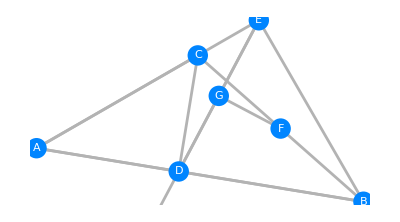
{9.23526,-Graphics-}

```mathematica
FindGeometricSceneGraphics@hyp001//Timing
```

```mathematica
graph001=%9[[2]]
```

-Graphics-

```mathematica
FindGeometricConjectures[graph001,Infinity,"Diagram"]
```

12345678910111213

Example 2/110

```mathematica
hyp002={
Triangle[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"]}],
GeometricPoint["O"]==RegionCenter[Triangle[GeometricPoint/@{"A","B","C"}],"Circumcenter"],
GeometricPoint["A1"]==Midpoint[Line[{GeometricPoint["B"],GeometricPoint["C"]}]],
GeometricPoint["B1"]==Midpoint[Line[{GeometricPoint["A"],GeometricPoint["C"]}]],
GeometricPoint["C1"]==Midpoint[Line[{GeometricPoint["A"],GeometricPoint["B"]}]]
		}
```

{Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],GeometricPoint[O]==RegionCenter[Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],Circumcenter],GeometricPoint[A1]==Midpoint[Line[{GeometricPoint[B],GeometricPoint[C]}]],GeometricPoint[B1]==Midpoint[Line[{GeometricPoint[A],GeometricPoint[C]}]],GeometricPoint[C1]==Midpoint[Line[{GeometricPoint[A],GeometricPoint[B]}]]}

```mathematica
Coords002=FindGeometricCoordinates@hyp002//Timing
```

{0.140401,{GeometricPoint[B]→{2.14844,2.65319},GeometricPoint[C]→{0.953079,0.97058},GeometricPoint[A]→{1.10993,0.0583537},GeometricPoint[O]→{2.91997,0.839169},GeometricPoint[A1]→{1.55076,1.81188},GeometricPoint[B1]→{1.0315,0.514467},GeometricPoint[C1]→{1.62918,1.35577}}}

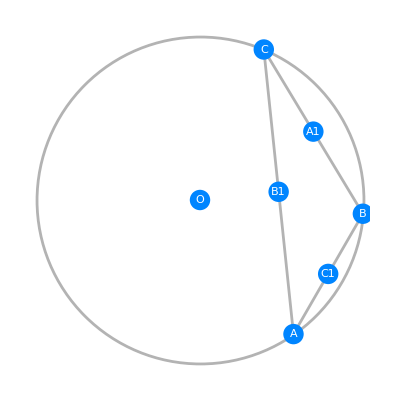
{0.109201,-Graphics-}

```mathematica
FindGeometricSceneGraphics@hyp002//Timing
```

```mathematica
graph002=%14[[2]]
```

-Graphics-

```mathematica
FindGeometricConjectures[graph002,Infinity,"Diagram"]
```

TabView[{},ControlPlacement→Left]

Example 3/110

```mathematica
hyp003={
Triangle[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"]}],
GeometricPoint["H"]==RegionCenter[Triangle[GeometricPoint/@{"A","B","C"}],"Orthocenter"],
Collinear[GeometricPoint["A"],GeometricPoint["H"],GeometricPoint["D"]],
Collinear[GeometricPoint["D"],GeometricPoint["B"],GeometricPoint["C"]],
Collinear[GeometricPoint["A"],GeometricPoint["C"],GeometricPoint["E"]],
Collinear[GeometricPoint["E"],GeometricPoint["B"],GeometricPoint["H"]],
Collinear[GeometricPoint["F"],GeometricPoint["A"],GeometricPoint["B"]],
Collinear[GeometricPoint["F"],GeometricPoint["C"],GeometricPoint["H"]],
GeometricPoint["P"]==Midpoint[Line[{GeometricPoint["B"],GeometricPoint["E"]}]],
GeometricPoint["Q"]==Midpoint[Line[{GeometricPoint["F"],GeometricPoint["C"]}]],
GeometricPoint["A1"]==Midpoint[Line[{GeometricPoint["B"],GeometricPoint["C"]}]],
GeometricPoint["O"]==RegionCenter[Triangle[GeometricPoint/@{"P","Q","D"}],"Circumcenter"]
		}
```

{Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],GeometricPoint[H]==RegionCenter[Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],Orthocenter],Collinear[GeometricPoint[A],GeometricPoint[H],GeometricPoint[D]],Collinear[GeometricPoint[D],GeometricPoint[B],GeometricPoint[C]],Collinear[GeometricPoint[A],GeometricPoint[C],GeometricPoint[E]],Collinear[GeometricPoint[E],GeometricPoint[B],GeometricPoint[H]],Collinear[GeometricPoint[F],GeometricPoint[A],GeometricPoint[B]],Collinear[GeometricPoint[F],GeometricPoint[C],GeometricPoint[H]],GeometricPoint[P]==Midpoint[Line[{GeometricPoint[B],GeometricPoint[E]}]],GeometricPoint[Q]==Midpoint[Line[{GeometricPoint[F],GeometricPoint[C]}]],GeometricPoint[A1]==Midpoint[Line[{GeometricPoint[B],GeometricPoint[C]}]],GeometricPoint[O]==RegionCenter[Triangle[{GeometricPoint[P],GeometricPoint[Q],GeometricPoint[D]}],Circumcenter]}

```mathematica
Coords003=FindGeometricCoordinates@hyp003//Timing
```

{1.95001,{GeometricPoint[B]→{0.135153,1.08005},GeometricPoint[E]→{1.65599,1.02053},GeometricPoint[F]→{0.610081,2.07131},GeometricPoint[C]→{1.67711,1.56008},GeometricPoint[A]→{1.79381,4.54198},GeometricPoint[D]→{2.62979,1.85666},GeometricPoint[H]→{2.90531,0.971635},GeometricPoint[P]→{0.895573,1.05029},GeometricPoint[Q]→{1.14359,1.8157},GeometricPoint[O]→{1.90572,1.14585},GeometricPoint[A1]→{0.906131,1.32007}}}

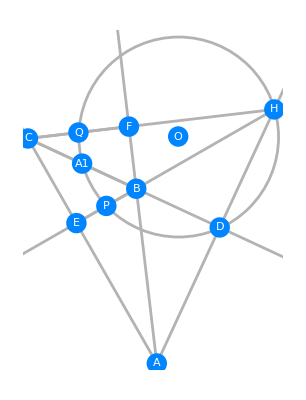
{12.9169,-Graphics-}

```mathematica
FindGeometricSceneGraphics@hyp003//Timing
```

```mathematica
graph003=%118[[2]]
```

-Graphics-

```mathematica
FindGeometricConjectures[graph003,Infinity,"Diagram"]
```

1234567891011121314151617181920212223242526272829

Example 4/110 (works great)

```mathematica
hyp004={
CircleThrough[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"],GeometricPoint["D"]}],
GeometricPoint["S"]==Midpoint[Line[{GeometricPoint["A"],GeometricPoint["D"]}]],
GeometricPoint["Q"]==Midpoint[Line[{GeometricPoint["B"],GeometricPoint["C"]}]],
Perpendicular[Line[{GeometricPoint["S"],GeometricPoint["M"]}],Line[{GeometricPoint["B"],GeometricPoint["C"]}]],
Perpendicular[Line[{GeometricPoint["Q"],GeometricPoint["M"]}],Line[{GeometricPoint["A"],GeometricPoint["D"]}]],
Collinear[GeometricPoint["B"],GeometricPoint["C"],GeometricPoint["I"]],
Collinear[GeometricPoint["A"],GeometricPoint["D"],GeometricPoint["I"]],
GeometricPoint["J"]==Midpoint[Line[{GeometricPoint["O"],GeometricPoint["M"]}]]
		}
```

{CircleThrough[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C],GeometricPoint[D]}],GeometricPoint[S]==Midpoint[Line[{GeometricPoint[A],GeometricPoint[D]}]],GeometricPoint[Q]==Midpoint[Line[{GeometricPoint[B],GeometricPoint[C]}]],Line[{GeometricPoint[S],GeometricPoint[M]}]⊥Line[{GeometricPoint[B],GeometricPoint[C]}],Line[{GeometricPoint[Q],GeometricPoint[M]}]⊥Line[{GeometricPoint[A],GeometricPoint[D]}],Collinear[GeometricPoint[B],GeometricPoint[C],GeometricPoint[I]],Collinear[GeometricPoint[A],GeometricPoint[D],GeometricPoint[I]],GeometricPoint[J]==Midpoint[Line[{GeometricPoint[O],GeometricPoint[M]}]]}

```mathematica
Coords004=FindGeometricCoordinates@hyp004//Timing
```

{1.23241,{GeometricPoint[A]→{1.10278,3.13732},GeometricPoint[D]→{0.544142,1.93234},GeometricPoint[B]→{1.19428,0.644802},GeometricPoint[C]→{2.16644,0.337676},GeometricPoint[Q]→{1.68036,0.491239},GeometricPoint[M]→{0.369798,1.09883},GeometricPoint[S]→{0.823463,2.53483},GeometricPoint[O]→{1.70316,0.292722},GeometricPoint[I]→{0.106543,0.988444},Unspecified[ref,{1,0},1]→{0.93151,0.887185},Unspecified[ref,{1,0},2]→{0.853569,0.984802},Unspecified[ref,{1,0},3]→{2.45013,0.369086},Unspecified[ref,{1,0},0]→{2.13403,1.92724},GeometricPoint[J]→{1.03648,0.695776}}}

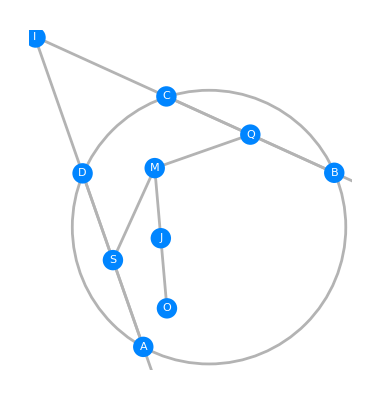
{1.38841,-Graphics-}

```mathematica
FindGeometricSceneGraphics@hyp004//Timing
```

```mathematica
graph004=%30[[2]]
```

-Graphics-

```mathematica
FindGeometricConjectures[graph004,Infinity,"Diagram"]
```

12345678

Example 5/110 (breaks down)

```mathematica
hyp005={
GeometricPoint["H"]==RegionCenter[Triangle[GeometricPoint/@{"A","B","C"}],"Orthocenter"],
GeometricPoint["O"]==RegionCenter[Triangle[GeometricPoint/@{"A","B","C"}],"Incenter"],
GeometricPoint["A1"]==RegionCenter[Triangle[GeometricPoint/@{"B","C","H"}],"Incenter"]
		}
```

{GeometricPoint[H]==RegionCenter[Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],Orthocenter],GeometricPoint[O]==RegionCenter[Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],Incenter],GeometricPoint[A1]==RegionCenter[Triangle[{GeometricPoint[B],GeometricPoint[C],GeometricPoint[H]}],Incenter]}

```mathematica
Coords005=FindGeometricCoordinates@hyp005//Timing
```

{56.488,{GeometricPoint[A]→{4.654,3.32755},Unspecified[inc,{{GeometricPoint[A],GeometricPoint[B]},GeometricPoint[C]}]→{1.9539,3.41607},GeometricPoint[B]→{-1.98753,3.54529},Unspecified[inc,{{GeometricPoint[A],GeometricPoint[C]},GeometricPoint[B]}]→{2.48612,1.71551},GeometricPoint[C]→{1.99965,1.35377},Unspecified[inc,{{GeometricPoint[B],GeometricPoint[C]},GeometricPoint[A]}]→{1.46839,1.64577},Unspecified[inc,{{GeometricPoint[B],GeometricPoint[C]},GeometricPoint[H]}]→{1.52955,1.61216},Unspecified[inc,{{GeometricPoint[B],GeometricPoint[H]},GeometricPoint[C]}]→{0.407269,0.324764},GeometricPoint[H]→{1.9001,-1.6828},Unspecified[inc,{{GeometricPoint[C],GeometricPoint[H]},GeometricPoint[B]}]→{1.98208,0.817627},GeometricPoint[O]→{1.92298,2.47283},GeometricPoint[A1]→{1.10858,0.846265}}}

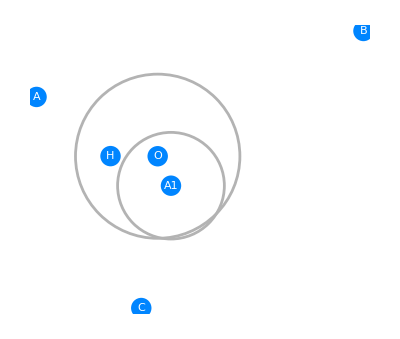
{91.6818,-Graphics-}

```mathematica
FindGeometricSceneGraphics@hyp005//Timing
```

```mathematica
graph005=%74[[2]]
```

-Graphics-

```mathematica
FindGeometricConjectures[graph005,Infinity,"Diagram"]
```

123

Example 6/110 (trivial, doesn’t show)

```mathematica
hyp006={
Triangle[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"]}],
GeometricPoint["H"]==RegionCenter[Triangle[GeometricPoint/@{"A","B","C"}],"Orthocenter"]
		}
```

{Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],GeometricPoint[H]==RegionCenter[Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],Orthocenter]}

```mathematica
Coords006=FindGeometricCoordinates@hyp004//Timing
```

{0.686404,{GeometricPoint[A]→{2.60909,0.874778},GeometricPoint[D]→{1.09292,0.694854},GeometricPoint[B]→{2.60909,0.874778},GeometricPoint[C]→{1.09292,0.694854},GeometricPoint[Q]→{1.85101,0.784816},GeometricPoint[M]→{1.59381,2.9522},GeometricPoint[S]→{1.85101,0.784816},GeometricPoint[O]→{1.91958,1.26964},GeometricPoint[I]→{-0.213483,0.539823},Unspecified[ref,{1,0},1]→{0.671894,1.39943},Unspecified[ref,{1,0},2]→{0.683208,1.33868},Unspecified[ref,{1,0},3]→{0.704304,1.25637},Unspecified[ref,{1,0},0]→{1.7578,1.57025},GeometricPoint[J]→{1.75669,2.11092}}}

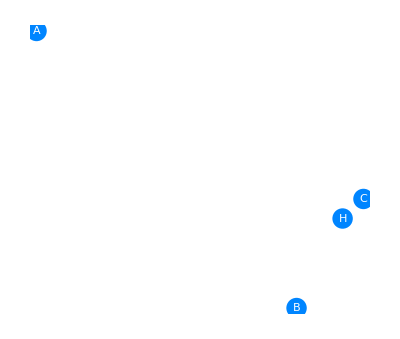
{0.109201,-Graphics-}

```mathematica
FindGeometricSceneGraphics@hyp006//Timing
```

```mathematica
graph006=%44[[2]]
```

-Graphics-

```mathematica
FindGeometricConjectures[graph006,Infinity,"Diagram"]
```

TabView[{},ControlPlacement→Left]

Example 7/110 (Simson-Wallace Theorem) does it work?

```mathematica
hyp007={
Triangle[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"]}],
CircleThrough[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"],GeometricPoint["P"]},GeometricPoint["O"]],
Collinear[GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["X"]],
Perpendicular[Line[{GeometricPoint["P"],GeometricPoint["X"]}],Line[{GeometricPoint["A"],GeometricPoint["B"]}]],
Collinear[GeometricPoint["A"],GeometricPoint["C"],GeometricPoint["Y"]],
Perpendicular[Line[{GeometricPoint["P"],GeometricPoint["Y"]}],Line[{GeometricPoint["A"],GeometricPoint["C"]}]],
Collinear[GeometricPoint["B"],GeometricPoint["C"],GeometricPoint["Z"]],
Perpendicular[Line[{GeometricPoint["P"],GeometricPoint["Z"]}],Line[{GeometricPoint["B"],GeometricPoint["C"]}]]
		}
```

{Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],CircleThrough[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C],GeometricPoint[P]},GeometricPoint[O]],Collinear[GeometricPoint[A],GeometricPoint[B],GeometricPoint[X]],Line[{GeometricPoint[P],GeometricPoint[X]}]⊥Line[{GeometricPoint[A],GeometricPoint[B]}],Collinear[GeometricPoint[A],GeometricPoint[C],GeometricPoint[Y]],Line[{GeometricPoint[P],GeometricPoint[Y]}]⊥Line[{GeometricPoint[A],GeometricPoint[C]}],Collinear[GeometricPoint[B],GeometricPoint[C],GeometricPoint[Z]],Line[{GeometricPoint[P],GeometricPoint[Z]}]⊥Line[{GeometricPoint[B],GeometricPoint[C]}]}

```mathematica
Coords007=FindGeometricCoordinates@hyp007//Timing
```

{0.577204,{GeometricPoint[A]→{1.47115,1.52263},GeometricPoint[B]→{1.46115,1.51528},GeometricPoint[C]→{1.46647,1.51851},GeometricPoint[P]→{1.42433,1.57515},GeometricPoint[X]→{1.46581,1.51871},GeometricPoint[Y]→{2.474,0.383326},GeometricPoint[Z]→{1.43996,1.54939},Unspecified[ref,{2,0},1]→{1.48071,1.5503},Unspecified[ref,{2,0},2]→{1.42206,1.57329},Unspecified[ref,{2,0},3]→{1.46453,1.57673},GeometricPoint[O]→{1.44557,1.54696}}}

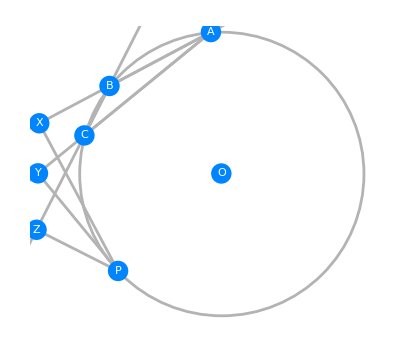
{5.02323,-Graphics-}

```mathematica
FindGeometricSceneGraphics@hyp007//Timing
```

```mathematica
graph007=%83[[2]]
```

-Graphics-

```mathematica
FindGeometricConjectures[graph007,Infinity,"Diagram"]
```

12345678

Example 8/110 (conjecture checker fails)

```mathematica
hyp008={
CircleThrough[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"],GeometricPoint["P"],GeometricPoint["P1"]}],
LineThrough[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["G"]}],
Perpendicular[Line[{GeometricPoint["A"],GeometricPoint["B"]}],Line[{GeometricPoint["P"],GeometricPoint["G"]}]],
LineThrough[{GeometricPoint["A"],GeometricPoint["C"],GeometricPoint["F"]}],
Perpendicular[Line[{GeometricPoint["A"],GeometricPoint["C"]}],Line[{GeometricPoint["P"],GeometricPoint["F"]}]],
LineThrough[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["G1"]}],
Perpendicular[Line[{GeometricPoint["A"],GeometricPoint["B"]}],Line[{GeometricPoint["P1"],GeometricPoint["G1"]}]],
LineThrough[{GeometricPoint["A"],GeometricPoint["C"],GeometricPoint["F1"]}],
Perpendicular[Line[{GeometricPoint["A"],GeometricPoint["C"]}],Line[{GeometricPoint["P1"],GeometricPoint["F1"]}]],
LineThrough[{GeometricPoint["F"],GeometricPoint["G"],GeometricPoint["K"]}],
LineThrough[{GeometricPoint["F1"],GeometricPoint["G1"],GeometricPoint["K"]}]
		}
```

{CircleThrough[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C],GeometricPoint[P],GeometricPoint[P1]}],LineThrough[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[G]}],Line[{GeometricPoint[A],GeometricPoint[B]}]⊥Line[{GeometricPoint[P],GeometricPoint[G]}],LineThrough[{GeometricPoint[A],GeometricPoint[C],GeometricPoint[F]}],Line[{GeometricPoint[A],GeometricPoint[C]}]⊥Line[{GeometricPoint[P],GeometricPoint[F]}],LineThrough[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[G1]}],Line[{GeometricPoint[A],GeometricPoint[B]}]⊥Line[{GeometricPoint[P1],GeometricPoint[G1]}],LineThrough[{GeometricPoint[A],GeometricPoint[C],GeometricPoint[F1]}],Line[{GeometricPoint[A],GeometricPoint[C]}]⊥Line[{GeometricPoint[P1],GeometricPoint[F1]}],LineThrough[{GeometricPoint[F],GeometricPoint[G],GeometricPoint[K]}],LineThrough[{GeometricPoint[F1],GeometricPoint[G1],GeometricPoint[K]}]}

```mathematica
Coords004=FindGeometricCoordinates@hyp008//Timing
```

{3.82202,{GeometricPoint[A]→{1.24765,0.774707},GeometricPoint[B]→{1.23926,0.775707},GeometricPoint[C]→{1.25603,0.773734},GeometricPoint[P]→{1.72764,5.95714},GeometricPoint[F]→{1.81858,6.74126},GeometricPoint[G]→{1.11146,0.790958},GeometricPoint[P1]→{2.55449,5.7622},GeometricPoint[F1]→{1.96446,0.675065},GeometricPoint[G1]→{1.92298,0.467504},GeometricPoint[K]→{-0.17353,-10.0219},Unspecified[ref,{1,0},1]→{2.39299,0.896561},Unspecified[ref,{1,0},2]→{2.05985,0.806953},Unspecified[ref,{1,0},3]→{2.55099,0.95631},Unspecified[ref,{1,0},0]→{1.55175,3.35998}}}

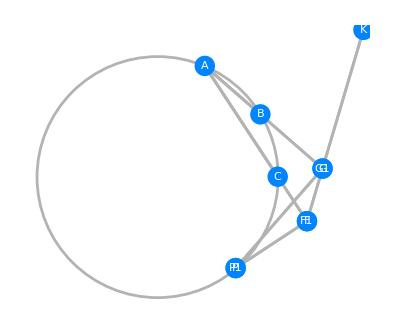
{3.33842,-Graphics-}

```mathematica
FindGeometricSceneGraphics@hyp008//Timing
```

```mathematica
graph008=%88[[2]]
```

-Graphics-

```mathematica
FindGeometricConjectures[graph008,Infinity,"Diagram"]
```

Function::fpct: Too many parameters in {GeometrySceneDrawer`Common`a$,PlaneGeometry`GeometryConjectureNewDump`o$,GeometrySceneDrawer`Common`b$} to be filled from Function[{GeometrySceneDrawer`Common`a$,PlaneGeometry`GeometryConjectureNewDump`o$,GeometrySceneDrawer`Common`b$},(Min[#1,2 π-#1]&)[First[Abs[Lookup[PlaneGeometry`GeometryConjectureNewDump`dirs$209882,{{«2»}},PlaneGeometry`GeometryConjectureNewDump`dirs$209882[«1»]+Times[«2»]]-Lookup[PlaneGeometry`GeometryConjectureNewDump`dirs$209882,{«1»},Plus[«2»]]]]]][GeometricPoint[G],GeometricPoint[G1]].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

Part::partw: Part {1,2,3} of {GeometricPoint[P],GeometricPoint[P1]} does not exist.

Part::partw: Part {3,2,1} of {GeometricPoint[P],GeometricPoint[P1]} does not exist.

Part::partw: Part {1,2,3} of {GeometricPoint[F],GeometricPoint[F1]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Gather::smtst: Application of the SameTest function yielded (Chop[First[Lookup[GeometrySceneDrawer`Common`segs$209882,{Part[«2»]},GeometrySceneDrawer`Common`segs$209882[Part[«2»]]]]-First[Lookup[GeometrySceneDrawer`Common`segs$209882,{«1»},GeometrySceneDrawer`Common`segs$209882[«1»]]],GeometrySceneDrawer`Common`ϵ$209882]==0&)[{GeometricPoint[G]-GeometricPoint[G1]+GeometricPoint[P],GeometricPoint[G1],GeometricPoint[G1]},{«1»}], which evaluates to Missing[KeyAbsent,{GeometricPoint[G1],GeometricPoint[G]-GeometricPoint[G1]+GeometricPoint[P]}]-Missing[KeyAbsent,{GeometricPoint[G1],GeometricPoint[G]-GeometricPoint[«1»]+GeometricPoint[P1]}]==0. The SameTest function must evaluate to True or False at every pair of elements.

Gather::smtst: Application of the SameTest function yielded (Chop[First[Lookup[GeometrySceneDrawer`Common`segs$209882,{Part[«2»]},GeometrySceneDrawer`Common`segs$209882[Part[«2»]]]]-First[Lookup[GeometrySceneDrawer`Common`segs$209882,{«1»},GeometrySceneDrawer`Common`segs$209882[«1»]]],GeometrySceneDrawer`Common`ϵ$209882]==0&)[{-GeometricPoint[G]+GeometricPoint[G1]+GeometricPoint[P],GeometricPoint[G],GeometricPoint[G]},{«1»}], which evaluates to Missing[KeyAbsent,{GeometricPoint[G],-GeometricPoint[G]+GeometricPoint[G1]+GeometricPoint[P]}]-Missing[KeyAbsent,{GeometricPoint[G],-GeometricPoint[«1»]+GeometricPoint[G1]+GeometricPoint[P1]}]==0. The SameTest function must evaluate to True or False at every pair of elements.

Gather::smtst: Application of the SameTest function yielded (Chop[First[Lookup[GeometrySceneDrawer`Common`segs$209882,{Part[«2»]},GeometrySceneDrawer`Common`segs$209882[Part[«2»]]]]-First[Lookup[GeometrySceneDrawer`Common`segs$209882,{«1»},GeometrySceneDrawer`Common`segs$209882[«1»]]],GeometrySceneDrawer`Common`ϵ$209882]==0&)[{GeometricPoint[F]+GeometricPoint[G]-GeometricPoint[G1],GeometricPoint[G1],GeometricPoint[G1]},{«1»}], which evaluates to Missing[KeyAbsent,{GeometricPoint[G1],GeometricPoint[F]+GeometricPoint[G]-GeometricPoint[G1]}]-Missing[KeyAbsent,{GeometricPoint[G1],GeometricPoint[F1]+GeometricPoint[G]-GeometricPoint[«1»]}]==0. The SameTest function must evaluate to True or False at every pair of elements.

General::stop: Further output of Gather::smtst will be suppressed during this calculation.

123456789101112131415161718192021222324252627282930313233343536373839404142434445464748495051525354555657585960616263646566676869707172737475767778798081828384858687888990919293949596979899100101102103104105106107108109110111112113114115116117118119120121122123124125126127128129130131132133134135136137138139140141142143144145146147148149150151152153154155156157158159160161162163164165166167168169170171172173174175176

Example 9/110 (conjecture checker fails)

```mathematica
hyp009={
CircleThrough[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"],GeometricPoint["D"],GeometricPoint["P"],GeometricPoint["P1"]}],
LineThrough[{GeometricPoint["A"],GeometricPoint["C"],GeometricPoint["F"]}],
Perpendicular[Line[{GeometricPoint["P"],GeometricPoint["F"]}],Line[{GeometricPoint["A"],GeometricPoint["C"]}]],
LineThrough[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["G"]}],
Perpendicular[Line[{GeometricPoint["A"],GeometricPoint["B"]}],Line[{GeometricPoint["P"],GeometricPoint["G"]}]],
LineThrough[{GeometricPoint["A"],GeometricPoint["D"],GeometricPoint["F1"]}],
Perpendicular[Line[{GeometricPoint["A"],GeometricPoint["D"]}],Line[{GeometricPoint["P"],GeometricPoint["F1"]}]],
LineThrough[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["G1"]}],
Perpendicular[Line[{GeometricPoint["A"],GeometricPoint["B"]}],Line[{GeometricPoint["P1"],GeometricPoint["G1"]}]],
LineThrough[{GeometricPoint["A"],GeometricPoint["C"],GeometricPoint["F2"]}],
Perpendicular[Line[{GeometricPoint["A"],GeometricPoint["C"]}],Line[{GeometricPoint["P1"],GeometricPoint["F2"]}]],
LineThrough[{GeometricPoint["A"],GeometricPoint["D"],GeometricPoint["F3"]}],
Perpendicular[Line[{GeometricPoint["A"],GeometricPoint["D"]}],Line[{GeometricPoint["P1"],GeometricPoint["F3"]}]]
		}
```

{CircleThrough[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C],GeometricPoint[D],GeometricPoint[P],GeometricPoint[P1]}],LineThrough[{GeometricPoint[A],GeometricPoint[C],GeometricPoint[F]}],Line[{GeometricPoint[P],GeometricPoint[F]}]⊥Line[{GeometricPoint[A],GeometricPoint[C]}],LineThrough[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[G]}],Line[{GeometricPoint[A],GeometricPoint[B]}]⊥Line[{GeometricPoint[P],GeometricPoint[G]}],LineThrough[{GeometricPoint[A],GeometricPoint[D],GeometricPoint[F1]}],Line[{GeometricPoint[A],GeometricPoint[D]}]⊥Line[{GeometricPoint[P],GeometricPoint[F1]}],LineThrough[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[G1]}],Line[{GeometricPoint[A],GeometricPoint[B]}]⊥Line[{GeometricPoint[P1],GeometricPoint[G1]}],LineThrough[{GeometricPoint[A],GeometricPoint[C],GeometricPoint[F2]}],Line[{GeometricPoint[A],GeometricPoint[C]}]⊥Line[{GeometricPoint[P1],GeometricPoint[F2]}],LineThrough[{GeometricPoint[A],GeometricPoint[D],GeometricPoint[F3]}],Line[{GeometricPoint[A],GeometricPoint[D]}]⊥Line[{GeometricPoint[P1],GeometricPoint[F3]}]}

```mathematica
Coords009=FindGeometricCoordinates@hyp009//Timing
```

{1.04521,{GeometricPoint[A]→{2.89892,3.74357},GeometricPoint[B]→{1.2999,2.15718},GeometricPoint[C]→{1.37978,2.36982},GeometricPoint[D]→{1.28498,2.10947},GeometricPoint[P]→{1.77792,-0.205242},GeometricPoint[F]→{0.317764,1.40945},GeometricPoint[F1]→{0.371126,1.18418},GeometricPoint[G]→{0.359631,1.22434},GeometricPoint[P1]→{1.7947,-0.224467},GeometricPoint[F2]→{0.317431,1.40915},GeometricPoint[F3]→{0.3698,1.18284},GeometricPoint[G1]→{0.358475,1.22319},Unspecified[ref,{1,0},1]→{1.25824,0.787246},Unspecified[ref,{1,0},2]→{1.32547,2.23202},Unspecified[ref,{1,0},3]→{1.25261,1.9915},Unspecified[ref,{1,0},0]→{3.63703,1.40051}}}

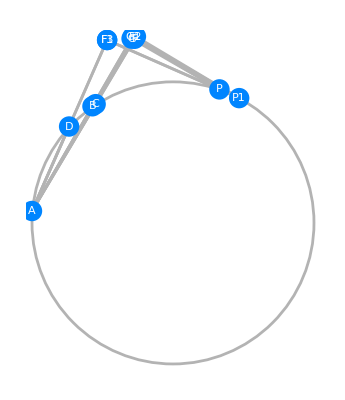
{47.7675,-Graphics-}

```mathematica
FindGeometricSceneGraphics@hyp009//Timing
```

```mathematica
graph009=%108[[2]]
```

-Graphics-

```mathematica
FindGeometricConjectures[graph009,Infinity,"Diagram"]
```

12345678910111213

Example 10/110 (misleading statement)

```mathematica
hyp010={
LineThrough[{GeometricPoint["Aprime"],GeometricPoint["B"],GeometricPoint["C"]}],
LineThrough[{GeometricPoint["Bprime"],GeometricPoint["A"],GeometricPoint["C"]}],
LineThrough[{GeometricPoint["Cprime"],GeometricPoint["A"],GeometricPoint["B"]}],
GeometricPoint["Oa"]==RegionCenter[Triangle[GeometricPoint/@{"A","Bprime","Cprime"}],"Orthocenter"],
GeometricPoint["Ob"]==RegionCenter[Triangle[GeometricPoint/@{"Aprime","B","Cprime"}],"Orthocenter"],
GeometricPoint["Oc"]==RegionCenter[Triangle[GeometricPoint/@{"Aprime","Bprime","C"}],"Orthocenter"]
		}
```

{LineThrough[{GeometricPoint[Aprime],GeometricPoint[B],GeometricPoint[C]}],LineThrough[{GeometricPoint[Bprime],GeometricPoint[A],GeometricPoint[C]}],LineThrough[{GeometricPoint[Cprime],GeometricPoint[A],GeometricPoint[B]}],GeometricPoint[Oa]==RegionCenter[Triangle[{GeometricPoint[A],GeometricPoint[Bprime],GeometricPoint[Cprime]}],Orthocenter],GeometricPoint[Ob]==RegionCenter[Triangle[{GeometricPoint[Aprime],GeometricPoint[B],GeometricPoint[Cprime]}],Orthocenter],GeometricPoint[Oc]==RegionCenter[Triangle[{GeometricPoint[Aprime],GeometricPoint[Bprime],GeometricPoint[C]}],Orthocenter]}

```mathematica
Coords010=FindGeometricCoordinates@hyp010//Timing
```

{0.702005,{GeometricPoint[Aprime]→{5.06319,3.8889},GeometricPoint[B]→{1.10838,8.35239},GeometricPoint[C]→{1.08023,8.38416},GeometricPoint[Bprime]→{5.23034,3.93578},GeometricPoint[A]→{1.19995,8.25466},GeometricPoint[Cprime]→{5.15293,3.98401},GeometricPoint[Oa]→{-10.6529,-10.766},GeometricPoint[Ob]→{5.45479,4.25147},GeometricPoint[Oc]→{2.90549,1.87587}}}

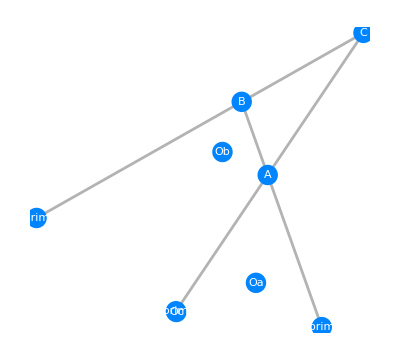
{0.187201,-Graphics-}

```mathematica
FindGeometricSceneGraphics@hyp010//Timing
```

```mathematica
graph010=%145[[2]]
```

-Graphics-

```mathematica
FindGeometricConjectures[graph010,Infinity,"Diagram"]
```

12

Example 11/110

```mathematica
hyp011={
GeometricPoint["L"]==Midpoint[Line[{GeometricPoint["A"],GeometricPoint["B"]}]],
GeometricPoint["M"]==Midpoint[Line[{GeometricPoint["B"],GeometricPoint["C"]}]],
GeometricPoint["N"]==Midpoint[Line[{GeometricPoint["A"],GeometricPoint["C"]}]],
Perpendicular[Line[{GeometricPoint["A"],GeometricPoint["D"]}],Line[{GeometricPoint["B"],GeometricPoint["C"]}]],
LineThrough[{GeometricPoint["B"],GeometricPoint["D"],GeometricPoint["C"]}],
CircleThrough[{GeometricPoint["M"],GeometricPoint["N"],GeometricPoint["L"]}]
		}
```

{GeometricPoint[L]==Midpoint[Line[{GeometricPoint[A],GeometricPoint[B]}]],GeometricPoint[M]==Midpoint[Line[{GeometricPoint[B],GeometricPoint[C]}]],GeometricPoint[N]==Midpoint[Line[{GeometricPoint[A],GeometricPoint[C]}]],Line[{GeometricPoint[A],GeometricPoint[D]}]⊥Line[{GeometricPoint[B],GeometricPoint[C]}],LineThrough[{GeometricPoint[B],GeometricPoint[D],GeometricPoint[C]}],CircleThrough[{GeometricPoint[M],GeometricPoint[N],GeometricPoint[L]}]}

```mathematica
Coords011=FindGeometricCoordinates@hyp011//Timing
```

{0.234002,{GeometricPoint[A]→{1.64692,2.83363},GeometricPoint[D]→{1.59328,1.1638},GeometricPoint[B]→{-0.586857,1.23382},GeometricPoint[C]→{2.56388,1.13262},GeometricPoint[L]→{0.53003,2.03372},GeometricPoint[M]→{0.988511,1.18322},GeometricPoint[N]→{2.1054,1.98312},Unspecified[ref,{6,0},1]→{1.85633,2.48882},Unspecified[ref,{6,0},2]→{1.38952,1.11682},Unspecified[ref,{6,0},3]→{1.8773,1.347},Unspecified[ref,{6,0},0]→{1.31448,1.90777}}}

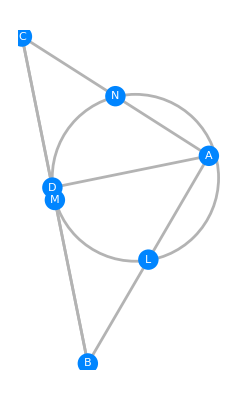
{0.327602,-Graphics-}

```mathematica
FindGeometricSceneGraphics@hyp011//Timing
```

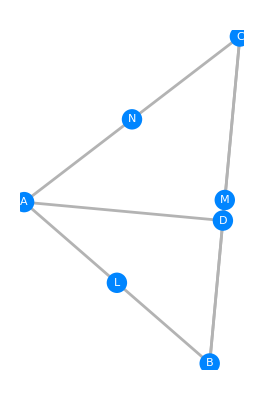

```mathematica
graph011=%306[[2]]
```

```mathematica
FindGeometricConjectures[graph011,Infinity,"Diagram"]
```

1234

Example 12/110 (serious cluster problem)

```mathematica
hyp012={
CircleThrough[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"],GeometricPoint["D"]}],
LineThrough[{GeometricPoint["A"],GeometricPoint["C"],GeometricPoint["M"]}],
LineThrough[{GeometricPoint["B"],GeometricPoint["D"],GeometricPoint["M"]}],
LineThrough[{GeometricPoint["B"],GeometricPoint["C"],GeometricPoint["E"]}],
Perpendicular[Line[{GeometricPoint["M"],GeometricPoint["E"]}],Line[{GeometricPoint["B"],GeometricPoint["C"]}]],
LineThrough[{GeometricPoint["A"],GeometricPoint["D"],GeometricPoint["F"]}],
LineThrough[{GeometricPoint["E"],GeometricPoint["F"],GeometricPoint["M"]}]
		}
```

{CircleThrough[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C],GeometricPoint[D]}],LineThrough[{GeometricPoint[A],GeometricPoint[C],GeometricPoint[M]}],LineThrough[{GeometricPoint[B],GeometricPoint[D],GeometricPoint[M]}],LineThrough[{GeometricPoint[B],GeometricPoint[C],GeometricPoint[E]}],Line[{GeometricPoint[M],GeometricPoint[E]}]⊥Line[{GeometricPoint[B],GeometricPoint[C]}],LineThrough[{GeometricPoint[A],GeometricPoint[D],GeometricPoint[F]}],LineThrough[{GeometricPoint[E],GeometricPoint[F],GeometricPoint[M]}]}

```mathematica
Coords012=FindGeometricCoordinates@hyp012//Timing
```

{0.436803,{GeometricPoint[B]→{1.10707,4.41776},GeometricPoint[C]→{1.09986,4.26861},GeometricPoint[M]→{0.559758,-4.66945},GeometricPoint[E]→{0.724605,-4.67743},GeometricPoint[A]→{1.10996,4.45181},GeometricPoint[D]→{1.10033,4.28913},GeometricPoint[F]→{0.625566,-4.67264},Unspecified[ref,{1,0},1]→{2.29146,2.07449},Unspecified[ref,{1,0},2]→{2.83145,1.82111},Unspecified[ref,{1,0},3]→{1.80565,2.46805},Unspecified[ref,{1,0},0]→{3.62809,4.22103}}}

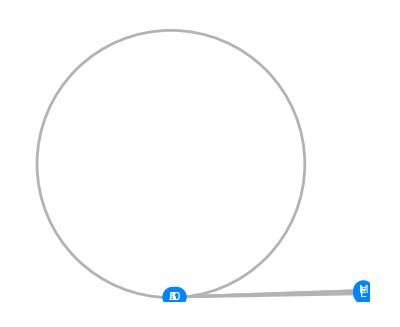
{1.74721,-Graphics-}

```mathematica
FindGeometricSceneGraphics@hyp012//Timing
```

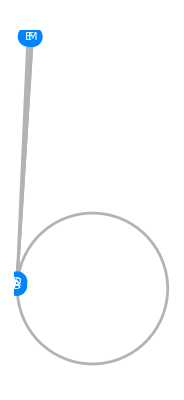

```mathematica
graph012=%203[[2]]
```

```mathematica
FindGeometricConjectures[graph012,Infinity,"Diagram"]
```

123

Example 13/110

```mathematica
hyp013={
Parallel[Line[{GeometricPoint["A"],GeometricPoint["B"]}],Line[{GeometricPoint["C"],GeometricPoint["D"]}]],
Parallel[Line[{GeometricPoint["A"],GeometricPoint["D"]}],Line[{GeometricPoint["B"],GeometricPoint["C"]}]],
LineThrough[{GeometricPoint["A"],GeometricPoint["Oa"],GeometricPoint["C"]}],
LineThrough[{GeometricPoint["B"],GeometricPoint["Ob"],GeometricPoint["D"]}],
LineThrough[{GeometricPoint["C"],GeometricPoint["Oc"],GeometricPoint["A"]}],
LineThrough[{GeometricPoint["D"],GeometricPoint["Od"],GeometricPoint["B"]}],
Perpendicular[Line[{GeometricPoint["A"],GeometricPoint["Od"]}],Line[{GeometricPoint["B"],GeometricPoint["D"]}]],
Perpendicular[Line[{GeometricPoint["B"],GeometricPoint["Oc"]}],Line[{GeometricPoint["A"],GeometricPoint["C"]}]],
Perpendicular[Line[{GeometricPoint["C"],GeometricPoint["Ob"]}],Line[{GeometricPoint["B"],GeometricPoint["D"]}]],
Perpendicular[Line[{GeometricPoint["D"],GeometricPoint["Oa"]}],Line[{GeometricPoint["A"],GeometricPoint["C"]}]]
		}
```

{Parallel[Line[{GeometricPoint[A],GeometricPoint[B]}],Line[{GeometricPoint[C],GeometricPoint[D]}]],Parallel[Line[{GeometricPoint[A],GeometricPoint[D]}],Line[{GeometricPoint[B],GeometricPoint[C]}]],LineThrough[{GeometricPoint[A],GeometricPoint[Oa],GeometricPoint[C]}],LineThrough[{GeometricPoint[B],GeometricPoint[Ob],GeometricPoint[D]}],LineThrough[{GeometricPoint[C],GeometricPoint[Oc],GeometricPoint[A]}],LineThrough[{GeometricPoint[D],GeometricPoint[Od],GeometricPoint[B]}],Line[{GeometricPoint[A],GeometricPoint[Od]}]⊥Line[{GeometricPoint[B],GeometricPoint[D]}],Line[{GeometricPoint[B],GeometricPoint[Oc]}]⊥Line[{GeometricPoint[A],GeometricPoint[C]}],Line[{GeometricPoint[C],GeometricPoint[Ob]}]⊥Line[{GeometricPoint[B],GeometricPoint[D]}],Line[{GeometricPoint[D],GeometricPoint[Oa]}]⊥Line[{GeometricPoint[A],GeometricPoint[C]}]}

```mathematica
Coords013=FindGeometricCoordinates@hyp013//Timing
```

{0.234002,{GeometricPoint[A]→{0.0567618,1.8581},GeometricPoint[B]→{1.47218,0.323296},GeometricPoint[C]→{2.9249,1.81161},GeometricPoint[D]→{1.50947,3.34641},GeometricPoint[Od]→{1.4909,1.84041},GeometricPoint[Oc]→{1.49668,1.83476},GeometricPoint[Ob]→{1.49076,1.8293},GeometricPoint[Oa]→{1.48498,1.83495}}}

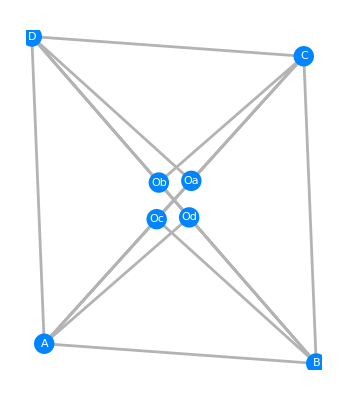
{1.37281,-Graphics-}

```mathematica
FindGeometricSceneGraphics@hyp013//Timing
```

```mathematica
graph013=%291[[2]]
```

-Graphics-

```mathematica
FindGeometricConjectures[graph013,Infinity,"Diagram"]
```

123456789101112131415161718192021222324252627282930313233343536373839404142434445464748

Example 14/110 (how do we set A and D in the circle?)

```mathematica
hyp014={
CircleThrough[{GeometricPoint["A"],GeometricPoint["E"]},GeometricPoint["P"]],
CircleThrough[{GeometricPoint["D"],GeometricPoint["E"]},GeometricPoint["Q"]],
Perpendicular[Line[{GeometricPoint["P"],GeometricPoint["E"]}],Line[{GeometricPoint["E"],GeometricPoint["Q"]}]],
Perpendicular[Line[{GeometricPoint["E"],GeometricPoint["F"]}],Line[{GeometricPoint["P"],GeometricPoint["Q"]}]],
Collinear[GeometricPoint["A"],GeometricPoint["D"],GeometricPoint["F"]]
		}
```

{CircleThrough[{GeometricPoint[A],GeometricPoint[E]},GeometricPoint[P]],CircleThrough[{GeometricPoint[D],GeometricPoint[E]},GeometricPoint[Q]],Line[{GeometricPoint[P],GeometricPoint[E]}]⊥Line[{GeometricPoint[E],GeometricPoint[Q]}],Line[{GeometricPoint[E],GeometricPoint[F]}]⊥Line[{GeometricPoint[P],GeometricPoint[Q]}],Collinear[GeometricPoint[A],GeometricPoint[D],GeometricPoint[F]]}

```mathematica
Coords014=FindGeometricCoordinates@hyp014//Timing
```

{0.156001,{GeometricPoint[E]→{2.04683,1.49933},GeometricPoint[F]→{0.715262,1.57214},GeometricPoint[Q]→{0.944213,0.198603},GeometricPoint[P]→{1.06103,2.33498},GeometricPoint[A]→{1.94311,1.3905},GeometricPoint[D]→{0.0766805,1.6666},Unspecified[ref,{1,0},1]→{1.1422,1.0452},Unspecified[ref,{1,0},2]→{0.336535,1.26483},Unspecified[ref,{1,0},3]→{0.0183442,3.09847},Unspecified[ref,{2,0},1]→{2.62511,0.485331},Unspecified[ref,{2,0},2]→{1.66831,1.74241},Unspecified[ref,{2,0},3]→{1.05163,1.9004}}}

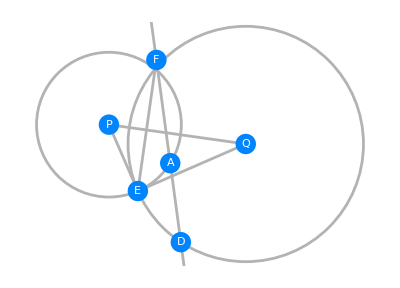
{0.140401,-Graphics-}

```mathematica
FindGeometricSceneGraphics@hyp014//Timing
```

```mathematica
graph014=%37[[2]]
```

-Graphics-

```mathematica
FindGeometricConjectures[graph014,Infinity,"Diagram"]
```

123

Example 15/110

```mathematica
hyp015={
Triangle[{GeometricPoint["A"],GeometricPoint["B"],GeometricPoint["C"]}],
Perpendicular[Line[{GeometricPoint["A"],GeometricPoint["D"]}],Line[{GeometricPoint["B"],GeometricPoint["C"]}]],
InfiniteLineThrough[{GeometricPoint["B"],GeometricPoint["D"],GeometricPoint["C"]}],Perpendicular[Line[{GeometricPoint["B"],GeometricPoint["E"]}],Line[{GeometricPoint["A"],GeometricPoint["C"]}]],
InfiniteLineThrough[{GeometricPoint["A"],GeometricPoint["E"],GeometricPoint["C"]}],
Perpendicular[Line[{GeometricPoint["C"],GeometricPoint["F"]}],Line[{GeometricPoint["A"],GeometricPoint["B"]}]],
InfiniteLineThrough[{GeometricPoint["A"],GeometricPoint["F"],GeometricPoint["B"]}],
Perpendicular[Line[{GeometricPoint["D"],GeometricPoint["I"]}],Line[{GeometricPoint["A"],GeometricPoint["B"]}]],
InfiniteLineThrough[{GeometricPoint["A"],GeometricPoint["I"],GeometricPoint["B"]}],
Perpendicular[Line[{GeometricPoint["F"],GeometricPoint["G"]}],Line[{GeometricPoint["B"],GeometricPoint["C"]}]],
InfiniteLineThrough[{GeometricPoint["B"],GeometricPoint["G"],GeometricPoint["C"]}],
Perpendicular[Line[{GeometricPoint["E"],GeometricPoint["K"]}],Line[{GeometricPoint["A"],GeometricPoint["B"]}]],
InfiniteLineThrough[{GeometricPoint["A"],GeometricPoint["K"],GeometricPoint["B"]}],
Perpendicular[Line[{GeometricPoint["F"],GeometricPoint["H"]}],Line[{GeometricPoint["A"],GeometricPoint["C"]}]],
InfiniteLineThrough[{GeometricPoint["A"],GeometricPoint["H"],GeometricPoint["C"]}],
CircleThrough[{GeometricPoint["I"],GeometricPoint["G"],GeometricPoint["K"]}]
		}
```

{Triangle[{GeometricPoint[A],GeometricPoint[B],GeometricPoint[C]}],Line[{GeometricPoint[A],GeometricPoint[D]}]⊥Line[{GeometricPoint[B],GeometricPoint[C]}],InfiniteLineThrough[{GeometricPoint[B],GeometricPoint[D],GeometricPoint[C]}],Line[{GeometricPoint[B],GeometricPoint[E]}]⊥Line[{GeometricPoint[A],GeometricPoint[C]}],InfiniteLineThrough[{GeometricPoint[A],GeometricPoint[E],GeometricPoint[C]}],Line[{GeometricPoint[C],GeometricPoint[F]}]⊥Line[{GeometricPoint[A],GeometricPoint[B]}],InfiniteLineThrough[{GeometricPoint[A],GeometricPoint[F],GeometricPoint[B]}],Line[{GeometricPoint[D],GeometricPoint[I]}]⊥Line[{GeometricPoint[A],GeometricPoint[B]}],InfiniteLineThrough[{GeometricPoint[A],GeometricPoint[I],GeometricPoint[B]}],Line[{GeometricPoint[F],GeometricPoint[G]}]⊥Line[{GeometricPoint[B],GeometricPoint[C]}],InfiniteLineThrough[{GeometricPoint[B],GeometricPoint[G],GeometricPoint[C]}],Line[{GeometricPoint[E],GeometricPoint[K]}]⊥Line[{GeometricPoint[A],GeometricPoint[B]}],InfiniteLineThrough[{GeometricPoint[A],GeometricPoint[K],GeometricPoint[B]}],Line[{GeometricPoint[F],GeometricPoint[H]}]⊥Line[{GeometricPoint[A],GeometricPoint[C]}],InfiniteLineThrough[{GeometricPoint[A],GeometricPoint[H],GeometricPoint[C]}],CircleThrough[{GeometricPoint[I],GeometricPoint[G],GeometricPoint[K]}]}

```mathematica
Coords015=FindGeometricCoordinates@hyp015//Timing
```

{102.789,{GeometricPoint[A]→{3.2444,3.70224},GeometricPoint[B]→{-0.136271,1.07777},GeometricPoint[C]→{2.24868,1.54803},GeometricPoint[D]→{3.61601,1.81764},GeometricPoint[E]→{1.64974,0.252239},GeometricPoint[F]→{1.57964,2.40986},GeometricPoint[I]→{2.56338,3.17356},GeometricPoint[K]→{0.57825,1.63246},GeometricPoint[G]→{1.76825,1.4533},GeometricPoint[H]→{2.45913,2.00334},Unspecified[ref,{3,0},1]→{0.970774,1.29606},Unspecified[ref,{3,0},2]→{-0.908133,0.925574},Unspecified[ref,{11,0},1]→{2.88598,1.67369},Unspecified[ref,{11,0},2]→{4.38846,1.96995},Unspecified[ref,{5,0},1]→{1.3342,-0.430435},Unspecified[ref,{5,0},2]→{3.52996,4.32003},Unspecified[ref,{15,0},1]→{1.96535,0.935051},Unspecified[ref,{15,0},2]→{0.93911,-1.28519},Unspecified[ref,{7,0},1]→{-0.723075,0.622224},Unspecified[ref,{7,0},2]→{2.07315,2.79298},Unspecified[ref,{9,0},1]→{4.01355,4.29935},Unspecified[ref,{9,0},2]→{-2.0809,-0.431877},Unspecified[ref,{13,0},1]→{1.07985,2.02187},Unspecified[ref,{13,0},2]→{-1.35951,0.128147},Unspecified[ref,{16,0},1]→{0.967941,1.4393},Unspecified[ref,{16,0},2]→{2.31381,1.81081},Unspecified[ref,{16,0},3]→{1.90854,1.51034},Unspecified[ref,{16,0},0]→{1.34629,2.69223}}}

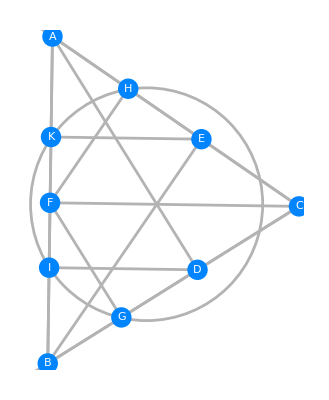
{38.813,-Graphics-}

```mathematica
FindGeometricSceneGraphics@hyp015//Timing
```

```mathematica
graph015=%164[[2]]
```

-Graphics-

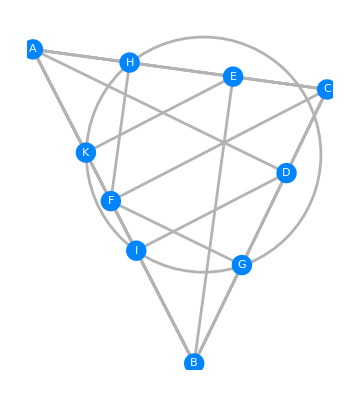

-Graphics-

```mathematica
FindGeometricConjectures[graph015,Infinity,"Diagram"]
```

12345678910111213141516171819202122

Example 16/110

```mathematica
hyp016={
Triangle[{GeometricPoint["O"],GeometricPoint["A"],GeometricPoint["B"]}],
GeometricPoint["M"]==Midpoint[Line[{GeometricPoint["A"],GeometricPoint["B"]}]],
Perpendicular[Line[{GeometricPoint["A"],GeometricPoint["C"]}],Line[{GeometricPoint["O"],GeometricPoint["B"]}]],
Collinear[GeometricPoint["B"],GeometricPoint["C"],GeometricPoint["O"]],
Perpendicular[Line[{GeometricPoint["B"],GeometricPoint["D"]}],Line[{GeometricPoint["O"],GeometricPoint["A"]}]],
Collinear[GeometricPoint["A"],GeometricPoint["D"],GeometricPoint["O"]],
Perpendicular[Line[{GeometricPoint["P"],GeometricPoint["M"]}],Line[{GeometricPoint["O"],GeometricPoint["A"]}]],
Collinear[GeometricPoint["A"],GeometricPoint["P"],GeometricPoint["O"]],
Perpendicular[Line[{GeometricPoint["Q"],GeometricPoint["M"]}],Line[{GeometricPoint["O"],GeometricPoint["B"]}]],
Collinear[GeometricPoint["O"],GeometricPoint["B"],GeometricPoint["Q"]],
Perpendicular[Line[{GeometricPoint["T"],GeometricPoint["Q"]}],Line[{GeometricPoint["O"],GeometricPoint["A"]}]],
Collinear[GeometricPoint["O"],GeometricPoint["A"],GeometricPoint["T"]],
Perpendicular[Line[{GeometricPoint["K"],GeometricPoint["P"]}],Line[{GeometricPoint["O"],GeometricPoint["B"]}]],
Collinear[GeometricPoint["B"],GeometricPoint["K"],GeometricPoint["O"]],
Collinear[GeometricPoint["T"],GeometricPoint["S"],GeometricPoint["Q"]],
Collinear[GeometricPoint["P"],GeometricPoint["S"],GeometricPoint["K"]]
		}
```

{Triangle[{GeometricPoint[O],GeometricPoint[A],GeometricPoint[B]}],GeometricPoint[M]==Midpoint[Line[{GeometricPoint[A],GeometricPoint[B]}]],Line[{GeometricPoint[A],GeometricPoint[C]}]⊥Line[{GeometricPoint[O],GeometricPoint[B]}],Collinear[GeometricPoint[B],GeometricPoint[C],GeometricPoint[O]],Line[{GeometricPoint[B],GeometricPoint[D]}]⊥Line[{GeometricPoint[O],GeometricPoint[A]}],Collinear[GeometricPoint[A],GeometricPoint[D],GeometricPoint[O]],Line[{GeometricPoint[P],GeometricPoint[M]}]⊥Line[{GeometricPoint[O],GeometricPoint[A]}],Collinear[GeometricPoint[A],GeometricPoint[P],GeometricPoint[O]],Line[{GeometricPoint[Q],GeometricPoint[M]}]⊥Line[{GeometricPoint[O],GeometricPoint[B]}],Collinear[GeometricPoint[O],GeometricPoint[B],GeometricPoint[Q]],Line[{GeometricPoint[T],GeometricPoint[Q]}]⊥Line[{GeometricPoint[O],GeometricPoint[A]}],Collinear[GeometricPoint[O],GeometricPoint[A],GeometricPoint[T]],Line[{GeometricPoint[K],GeometricPoint[P]}]⊥Line[{GeometricPoint[O],GeometricPoint[B]}],Collinear[GeometricPoint[B],GeometricPoint[K],GeometricPoint[O]],Collinear[GeometricPoint[T],GeometricPoint[S],GeometricPoint[Q]],Collinear[GeometricPoint[P],GeometricPoint[S],GeometricPoint[K]]}

```mathematica
Coords016=FindGeometricCoordinates@hyp016//Timing
```

{18.5485,{GeometricPoint[A]→{1.40817,2.81825},GeometricPoint[C]→{1.42124,2.81856},GeometricPoint[B]→{1.61076,-5.45863},GeometricPoint[D]→{1.42828,1.96331},GeometricPoint[K]→{1.53781,-2.27251},GeometricPoint[P]→{1.53288,-2.27262},GeometricPoint[O]→{1.41471,2.81841},GeometricPoint[M]→{1.50946,-1.32019},GeometricPoint[Q]→{1.516,-1.32003},GeometricPoint[T]→{1.2727,8.57623},GeometricPoint[S]→{1.27922,8.31091}}}

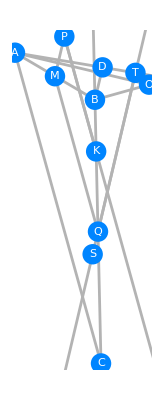
{8.00285,-Graphics-}

```mathematica
FindGeometricSceneGraphics@hyp016//Timing
```

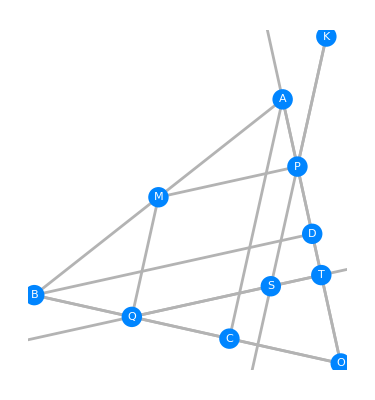

```mathematica
graph016=%155[[2]]
```

```mathematica
FindGeometricConjectures[graph016,Infinity,"Diagram"]
```

1234567891011121314151617181920212223242526272829303132